#### Expansion of functions at critical point

```mathematica
(*Defining functions*)
Clear[P,F,G,f,g,h,c,j,β1,β2,β3,β4,γ]
β1=1;
β2=1;
β3=1;
β4=1;
γ=-1;
f[T]= T;
g[T]= β2(1-T);
h[T]=1;
c[T]=2/3;
j[T]=-T^2/2 ;
(*f[T]= 1+α1(1-T);
g[T]= β1(1-T)+β2(1-T)^2;
h[T]=δ0+δ1(1-T);
c[T]=γ0+γ1(1-T)+γ2(1-T)^2;
j[T]=0 ;*)

(*Potentials and EOS*)
Integrate[(x-(f[T]-√g[T]))(x-(f[T]+√g[T])),x];
P[T_,x_]=h[T](%+c[T]);
F[T_,x_]=Integrate[1/x^2 P[T,x],x]+j[T];
G[T_,p_,x_]=F[T,x]+p/x//Simplify;
Temp[p_,x_]=T/.Solve[p==P[T,x],T][[1]];

(*xg-xl variables*)
Solve[P[T,xg]==P[T,xl],T][[2]];
Txgxl=1/2(-1+xg+xl+√((-1+xg+xl)^2-4(-1+1/3(xg^2+xl^2+xg*xl))));
Pxgxl=P[T,xg]/.T->Txgxl//Simplify;

(*Plotting functions*)
Manipulate[
Plot[{1,P[T,x]},{x,0,2}],
{T,0,1}
]
Manipulate[
Plot[G[T,p,x],{x,0,1}],
{p,0,1.5},{T,0,1.5}
]
```

#### Criteria on parameters for the existence of critical pressure

```mathematica
{Limit[D[P[T,f[T]+√g[T]],T],T->1]>0,Limit[D[P[T,f[T]-√g[T]],T],T->1]>0}
```

{True,True}

#### Loading xAct and defining the Ricci scalar*

```mathematica
<< xAct`xCoba`
$PrePrint = ScreenDollarIndices;
DefManifold[MCP,2,{u,v,w}]//Quiet;
DefChart[tX,MCP,{1,2},{t[],X[]}]//Quiet;
MetricCP=CTensor[DiagonalMatrix[{-D[F[T,x],{T,2}]/T,D[F[T,1/V],{V,2}]/(T*x^4)}/.{T->t[],V->1/x}/.{x-> X[]}],{-tX,-tX},0]//Quiet;
(*MetricCP=CTensor[DiagonalMatrix[{Normal[Series[D[F[T,x],{T,2}],{x,1,1}]],Normal[Series[Normal[Series[D[F[T,1/V],{V,2}],{V,1,1}]]/.V->1/x,{x,1,1}]]}/.{T->t[],V->1/x}/.{x-> X[]}],{-tX,-tX},0]//Quiet;*)
SetCMetric[MetricCP,tX,SignatureOfMetric->{2,0,0}]//Quiet;
CD=CovDOfMetric[MetricCP]//Quiet;

(*Constant symbols*)
DefConstantSymbol[γ]//Quiet;
DefConstantSymbol[β]//Quiet;
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,11,29}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold MCP.

** DefVBundle: Defining vbundle TangentMCP.

** DefChart: Defining chart tX.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar X[].

** DefMapping: Defining mapping tX.

** DefMapping: Defining inverse mapping itX.

** DefTensor: Defining mapping differential tensor ditX[-a,itXu].

** DefTensor: Defining mapping differential tensor dtX[-u,tXa].

** DefBasis: Defining basis tX. Coordinated basis.

** DefCovD: Defining parallel derivative PDtX[-u].

** DefTensor: Defining vanishing torsion tensor TorsionPDtX[u,-v,-w].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDtX[u,-v,-w].

** DefTensor: Defining vanishing Riemann tensor RiemannPDtX[-u,-v,-w,w1].

** DefTensor: Defining vanishing Ricci tensor RicciPDtX[-u,-v].

** DefTensor: Defining antisymmetric +1 density etaUptX[u,v].

** DefTensor: Defining antisymmetric -1 density etaDowntX[-u,-v].

** DefConstantSymbol: Defining constant symbol β.

-Graphics-

{0,0.5 (-1.-1. √(5.-4. x)+2. x),0.5 (-1.-1. √(5.-4. x)+2. x),0.5 (-1.+√(5.-4. x)+2. x),0.5 (-1.+√(5.-4. x)+2. x)}

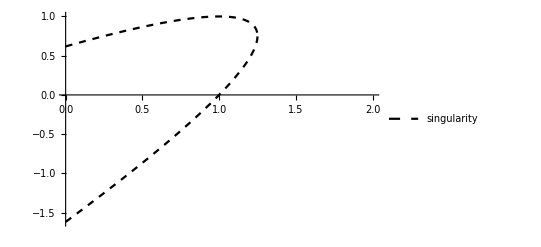

```mathematica
(*Solving the Ricci scalar field*)
RicciScalarField[T_,x_]=RicciScalar[CD][[1]]/.{t[]->T,X[]->x};
RicciPlot=ContourPlot[RicciScalarField[T,x],{x,0,2},{T,0,2},ColorFunction->"TemperatureMap",PlotLegends->Automatic,Contours->100,PlotRange->{{0,2},{0,2}}]
T/.NSolve[RicciScalarField[T,x]^-1==0,T]
SingularityPlot=Plot[{%[[2]],%[[4]]},{x,0,2},PlotStyle->{{Black,Dashed},{Black,Dashed}},PlotLegends->{"singularity"}]
```

#### Phase boundaries (Contour zeroes method)

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

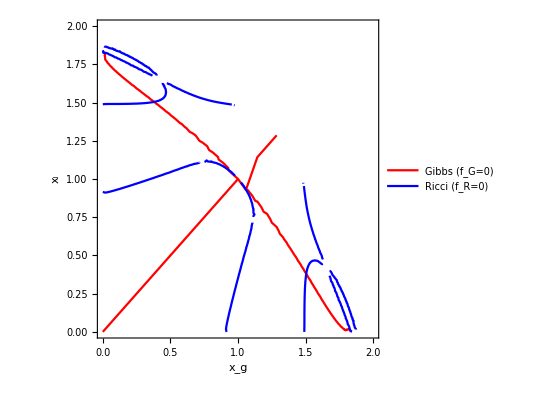

```mathematica
(*Equal Ricci contour*)
ZeroRicci=RicciScalarField[T,xg]-RicciScalarField[T,xl]/.{T->Txgxl,p->Pxgxl}//Simplify;
ZeroRiccifunc[xg_,xl_]=ZeroRicci;

(*Equal Gibbs contour*)
ZeroG=G[T,p,xg]-G[T,p,xl]/.{T->Txgxl,p->Pxgxl}//Simplify;
ZeroGfunc[xg_,xl_]=ZeroG;

(*Plotting*)
Show[
{ContourPlot[ZeroG==0,{xg,0,2},{xl,0,2},FrameLabel->{"x_g","x_l"},ContourStyle->{Red},PlotLegends->{"Gibbs (f_G=0)"}],
ContourPlot[ZeroRicci==0,{xg,0,2},{xl,0,2},FrameLabel->{"xg","xl"},ContourStyle->{Blue},PlotLegends->{"Ricci (f_R=0)"}]}
]
```

```mathematica
Manipulate[N[Txgxl/.{xg->xgas,xl-> xliq}],{xgas,0,1},{xliq,1,3}]
```

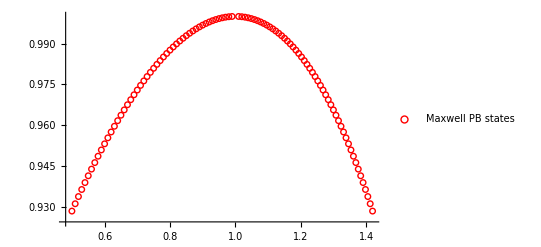

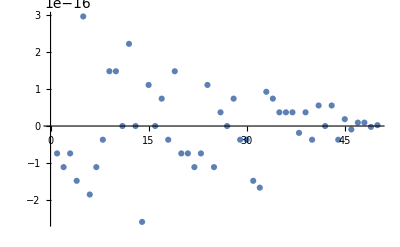

```mathematica
(*Maxwell phase boundary*)
PBPoints=Table[{Txgxl/.xg->xgas,xgas,xl}/.FindRoot[ZeroG==0/.xg->xgas,{xl,3-xgas}],{xgas,0.5,0.99,0.01}];
Table[{PBPoints[[n,2]],PBPoints[[n,1]]},{n,1,Length[PBPoints],1}];
Union[%,Table[{PBPoints[[n,3]],PBPoints[[n,1]]},{n,1,Length[PBPoints],1}]];
PBPlot=ListPlot[%,PlotStyle->Red,PlotLegends->{"Maxwell PB states"},PlotMarkers->{○}]

(*Difference in G*)
ListPlot[Table[ZeroGfunc[PBPoints[[n,2]],PBPoints[[n,3]]],{n,1,Length[PBPoints],1}]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

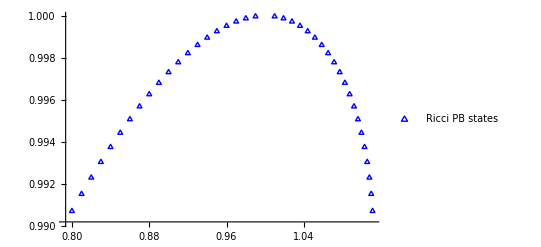

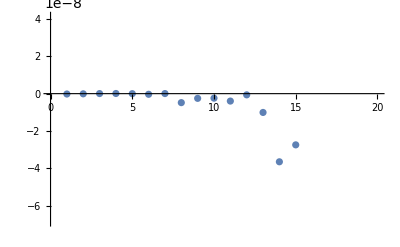

```mathematica
(*Ricci phase boundary*)
Clear[FitFunction]
FitFunction[x_]=-0.10078879160053286+3.177893031912354 x-2.076254268980525 x^2;
PBRPoints=Table[{Txgxl/.xg->xgas,xgas,xl}/.FindRoot[ZeroRicci==0/.xg->xgas,{xl,FitFunction[xgas]}],{xgas,0.8,1,0.01}];
Table[{PBRPoints[[n,2]],PBRPoints[[n,1]]},{n,1,Length[PBRPoints],1}];
Union[%,Table[{PBRPoints[[n,3]],PBRPoints[[n,1]]},{n,1,Length[PBRPoints],1}]];
PBRPlot=ListPlot[%,PlotStyle->{Blue,Triangle},PlotLegends->{"Ricci PB states"},PlotMarkers->{△}]

(*Difference in R*)
ListPlot[Table[RicciScalarField[PBRPoints[[n,1]],PBRPoints[[n,2]]]-RicciScalarField[PBRPoints[[n,1]],PBRPoints[[n,3]]],{n,1,Length[PBRPoints],1}]]
```

#### Widom line (Maximum CP on isobars)

```mathematica
Temp[p_,x_]=T/.Solve[p==P[T,x],T][[1]];
CP[p_,x_]=-T*D[F[T,x],{T,2}]-T D[P[T,x],T]^2/(D[P[T,x],x]*x^2)/.T->Temp[p,x];
(*WidomPoints=Table[
{x,Temp[p,x]}/.FindRoot[D[CP[p,x],x]==0,{x,1.01}],
{p,1.01,1.4,0.01}
];*)
```

```mathematica
(*Widom*)
Manipulate[Plot[CP[p,x],{x,0,3}],{p,1,10}]
```

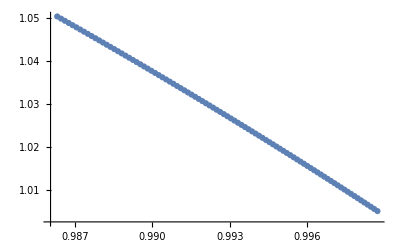

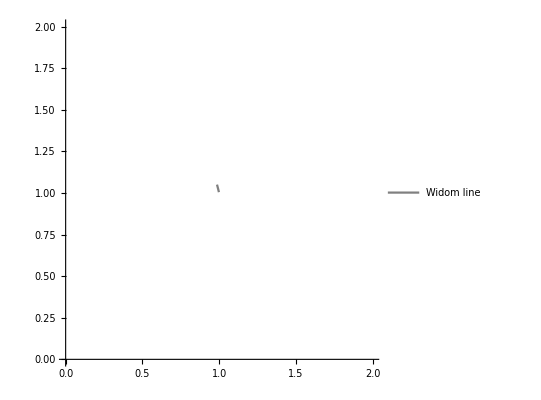

```mathematica
ListPlot[WidomPoints]

(*Smoothing the Widom line*)
ListInterpolation[Table[WidomPoints[[n,2]],{n,1,Length[WidomPoints]}]];
ListInterpolation[Table[WidomPoints[[n,1]],{n,1,Length[WidomPoints]}]];
WidomLineSmooth=ParametricPlot[{%[n],%%[n]},{n,1,Length[WidomPoints]},PlotRange->{{0,2},{0,2}},PlotStyle->{Gray},PlotLegends->{"Widom line"}]
```

#### Widom line (Ricci)

```mathematica
(*Ricci Widom*)
Manipulate[Plot[RicciScalarField[Temp[p,x],x],{x,0,3}],{p,1,10}]
```

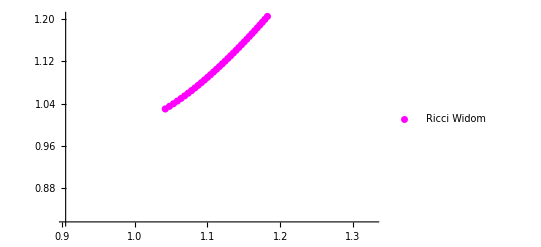

```mathematica
WidomRicciPoints=Table[
Re[{x,Temp[p,x]}]/.FindRoot[D[RicciScalarField[Temp[p,x],x],x]==0,{x,1.1}],
{p,1,1.4,0.01}
]//Quiet;

WidomRicciLine=ListPlot[WidomRicciPoints,PlotStyle->{Magenta},PlotLegends->{"Ricci Widom"}]
```

#### Plots

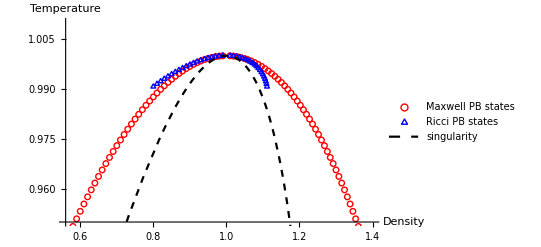

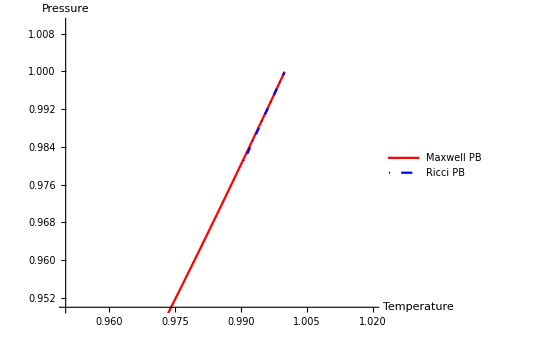

```mathematica
{PBPlot,PBRPlot,SingularityPlot};
Prepend[%,Plot[0,{x,-2,-1},PlotRange->{{0.56,1.4},{0.95,1.01}},AxesLabel->{"Density","Temperature"}]];
%//Show

(*Plotting Maxwell phase boundary in P-T plane*)
Table[{PBPoints[[n,1]],Pxgxl}/.{xg->PBPoints[[n,2]],xl->PBPoints[[n,3]]},{n,1,Length[PBPoints]}];
PBPTListPlot=ListPlot[%];
ListInterpolation[Table[%%[[n,2]],{n,1,Length[PBPoints]}]];
ListInterpolation[Table[%%%[[n,1]],{n,1,Length[PBPoints]}]];
PBPTSmooth=ParametricPlot[{%[n],%%[n]},{n,1,Length[PBPoints]},PlotStyle->{Red},PlotLegends->{"Maxwell PB"},PlotRange->{{0.95,1.02},{0.95,1.01}},AxesLabel->{"Temperature","Pressure"}];

(*Plotting Ricci phase boundary in P-T plane*)
Table[{PBRPoints[[n,1]],Pxgxl}/.{xg->PBRPoints[[n,2]],xl->PBRPoints[[n,3]]},{n,1,Length[PBRPoints]}];
PBPTRListPlot=ListPlot[%];
ListInterpolation[Table[%%[[n,2]],{n,1,Length[PBRPoints]}]];
ListInterpolation[Table[%%%[[n,1]],{n,1,Length[PBRPoints]}]];
PBPTRSmooth=ParametricPlot[{%[n],%%[n]},{n,1,Length[PBRPoints]},PlotStyle->{Blue,DotDashed},PlotLegends->{"Ricci PB"}];

(*Printing*)
Show[PBPTSmooth,PBPTRSmooth]
```

#### Sketch

```mathematica
FitFunction[x_]=Fit[Points,{1,x,x^2},x];
```

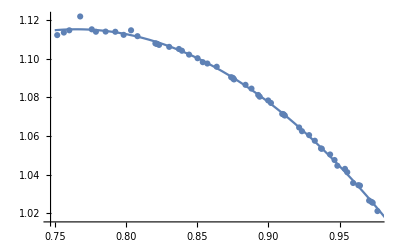

```mathematica
Show[{ListPlot[Points],Plot[Fit[Points,{1,x,x^2},x]/.x->T,{T,0.75,1}]}]
```

```mathematica
Points=ContourGraph[[1,1,1,1,1,3,1,12,1]];
```

```mathematica
ContourGraph=Flatten[FullForm[Normal[ContourPlot[ZeroRicci==0,{xg,0,2},{xl,0,2},FrameLabel->{"xg","xl"},ContourStyle->{Blue},PlotLegends->{"Ricci (f_R=0)"}]]]];//Quiet
```